### Quantum Measurement Simulation:

```mathematica
Quit
```

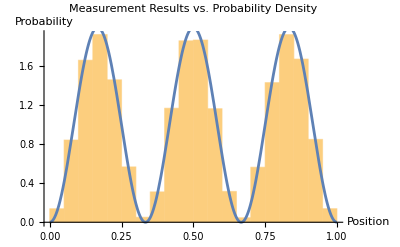

```mathematica
(*Simulating the collapse of the wave function upon measurement*)
n=3;L=1;
ψ[x_,n_,L_]:=Sqrt[2/L] Sin[n π x/L]

(*Create a function that generates random positions based on probability density*)
measurementDemo[numMeasurements_]:=Module[{results,pdf,dist},(*Define probability density function*)pdf[x_]:=ψ[x,n,L]^2;
(*Create a probability distribution*)dist=ProbabilityDistribution[pdf[x],{x,0,L}];
(*Generate random measurements according to the probability distribution*)results=RandomVariate[dist,numMeasurements];
(*Display results as a histogram with overlaid theoretical curve*)Histogram[results,20,"PDF",PlotLabel->"Measurement Results vs. Probability Density",AxesLabel->{"Position","Probability"},PlotRange->All,Epilog->{Red,Thick,Plot[pdf[x],{x,0,L},PlotRange->All][[1]]}]]

(*Run the simulation with 1000 measurements*)
measurementDemo[100000]
```